```mathematica
FullSimplify[DSolve[{ x''[t]==(q B)/m y'[t],y''[t]==-(q B)/m x'[t],x[0]==0,x'[0]== 3.1 10^4,y[0]==0,y'[0]== 0},{x[t],y[t]},t]]
```

{{x[t]→(31000. m Sin[(B q t)/m])/(B q),y[t]→(m (-31000.+31000. Cos[(B q t)/m]))/(B q)}}

```mathematica
(m (-31000.+31000. Cos[(B q t)/m]))/(B q)/.{m-> 1.67 10^-27, q->1.6 10^-19, B->10^-4}
```

0.000104375 (-31000.+31000. Cos[9580.84 t])

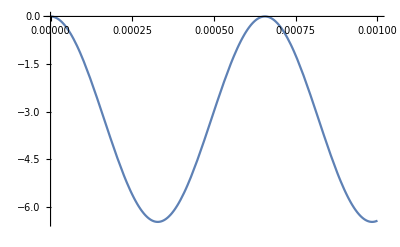

```mathematica
Plot[0.00010437499999999999 (-31000.+31000. Cos[9580.838323353295 t]),{t,0,10^-3}]
```